```mathematica
ClearAll["Global`*"]
```

```mathematica
f[x_]=(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)
g[x_]=A*UnitBox[x/b]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

A UnitBox[x/b]

```mathematica
c[y_]=Assuming[b>0,Convolve[g[x],f[x],x,y]]
```

1/2 A (Erf[(b+2 y-2 μ)/(2 √2 σ)]+Erf[(b-2 y+2 μ)/(2 √2 σ)])

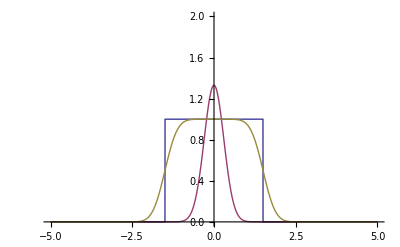

```mathematica
l={μ->0,σ->0.3,b->3,A->1};
Plot[{g[x]/.l,f[x]/.l,c[x]/.l},{x,-5,5},PlotRange->{0,2}]
```

```mathematica
imp=Import[ParentDirectory[NotebookDirectory[]]<>"\\data\\angles.txt","Table"]
```

{{180,329},{185,246},{190,42},{195,22},{200,21},{270,13},{175,291},{170,42},{165,35},{90,35}}

FittedModel[26.2335+151.902 (Erf[0.185125 (372.319-2 y)]+Erf[0.185125 (-345.8+2 y)])]

| Estimate | Standard Error | t-Statistic | P-Value
u | 26.2335 | 4.26378 | 6.15264 | 0.00164936
A | 303.804 | 10.8873 | 27.9045 | 1.10656×10^-6
b | 13.2595 | 0.473557 | 27.9997 | 1.08797×10^-6
μ | 179.53 | 0.156604 | 1146.39 | 9.58582×10^-15
σ | 1.90981 | 0.229152 | 8.33425 | 0.000406641

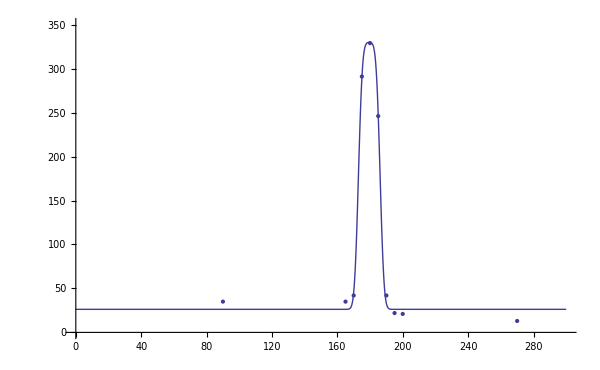

```mathematica
nlm=NonlinearModelFit[imp,1/2 A (Erf[(b+2 y-2 μ)/(2 √2 σ)]+Erf[(b-2 y+2 μ)/(2 √2 σ)])+u,{{u},{A,200},{b,20},{μ,180},σ},y]
nlm["ParameterTable"]
Show[Plot[Normal[nlm],{y,0,300},PlotRange->{0,350},ImageSize->600],ListPlot[imp]]
```